DrawPDpts converts a pd code into points. If it can be drawn with DrawPD it can be converted into points!
viewKnot[] is the same function used in my CPS project.
you can also use viewStickKnot[] (recommended)
viewKnot uses the ptsToTubes function also from my CPS project. Sometimes the ends don’t meet in viewKnot however so viewStickKnot is recommended so you are seeing the actual data and not a Bezier approximation.
If you would like to export the points, use exportPts[pts]. This produces a Mathematica MTX file which can be imported to the knot relaxer, and in theory, relaxed.

```mathematica
viewStickKnot[DrawPDpts[PD[X[1,6,2,7],X[3,8,4,9],X[5,10,6,1],X[7,2,8,3],X[9,4,10,5]]]]
```

-Graphics3D-

```mathematica
exportPts[DrawPDpts[PD[X[1,6,2,7],X[3,8,4,9],X[5,10,6,1],X[7,2,8,3],X[9,4,10,5]]]]
```

Get::path: ParentDirectory[File] in $Path is not a string.

General::stop: Further output of Get::path will be suppressed during this calculation.

ParentDirectory::nums: Argument File should be a positive machine-size integer, a nonempty string, or a File specification.

C:\Users\nth46038\Desktop\five1.mtx

```mathematica
viewKnot[DrawPDpts[PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]]]]
```

-Graphics3D-

```mathematica
exportPts[DrawPDpts[trefoil]]
```

```mathematica
(*a twelve crossing knot*)
viewStickKnot[DrawPDpts[PD[X[18,1,19,2],X[24,22,1,21],X[2,17,3,18],X[16,3,17,4],X[4,19,5,20],X[12,5,13,6],X[6,11,7,12],X[14,8,15,7],X[8,23,9,24],X[22,9,23,10],X[10,14,11,13],X[20,15,21,16]]]]
```

## This is a work in progress. You can start by evaluating initialization cells then reading the text above each initialization cell and evaluating examples.

The following cell contains general functions for adding changing the fields of a triangulation T represented by an array.
For a planar diagram D, each component of D (Crossings, Strands, Faces) is assigned a distinct circle represented by a number.
This number is a position in the array of T. Each element of T is another array with 5 elements. 
The first is a list of neighbouring components.
The second is what type of component it is, either “X”, “e”, or “f”. 
The third is the radius of the circle, some scalar. 
The fourth is the center of that circle represented as a complex number. 
The fifth contains the graphics objects.
Here is an example triangulation of the trefoil before being passed into the draw function. It has 14 components (3 crossings, 6 strands, 5 faces) and was passed into Column[] for clarity.

```mathematica
(*example usage of the neighbours variable.
this returns the neighboring circles of the first crossing of this trefoil*)
Triangulate[PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]]]⟦1,neighbours⟧
```

DrawPD breaks the process of adding components to a triangulation down into 5 phases.
The first phase is assigning each component a number and finding out which component is neighbour to which. This also determines the type of the component.
The second phase adds the radii of the circles.
The third phase adds  the positions of the circles.
The fourth phase manipulates the radii and positions until the knot is “balanced”.
The fifth phase adds the graphics objects to the triangulation so it can be drawn.
This next cell contains the utilities to help add and manipulate fields to the triangulation.

```mathematica
(*field values*)
neighbours=1;
type=2;
r=3;
centre=4;
graphicsObjs=5;

FieldValues[triangulation_,field_]:=
  Table[triangulation[[i,field]],{i,
      Length[triangulation]}]

AddField[triangulation_,field_,values_]:=
  Table[ReplacePart[
      If[Length[triangulation[[i]]]<
          field,PadRight[
          triangulation[[i]],field],
        triangulation[[i]]],
      values[[i]],field],{i,
      Length[triangulation]}]

ChangeField[triangulation_,field_,f_]:=
  MapAt[f,triangulation,Table[{i,field},{i,Length[triangulation]}]]

DeriveField[triangulation_,field_,f_]:=
  AddField[triangulation,field,Map[f,triangulation]]
```

#### Phase one: neighbours and types

```mathematica
(*Let's initialize some knots*)
trefoil =PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]];
figure8 = PD[X[4,2,5,1],X[8,6,1,5],X[6,3,7,4],X[2,7,3,8]];
five1 = PD[X[1,6,2,7],X[3,8,4,9],X[5,10,6,1],X[7,2,8,3],X[9,4,10,5]];
six1=PD[X[1,4,2,5],X[7,10,8,11],X[3,9,4,8],X[9,3,10,2],X[5,12,6,1],X[11,6,12,7]];
(*If you want to draw all knot theory knots we also have this*)
```

```mathematica
(*Every number in a PD code now has a distinct coordinate (c,n) that can be used to identify it.*)
List@@@List@@trefoil
```

```mathematica
(*calculates the coordinate of the other vertex of a strand*)
OtherVertex[trefoil,{1,2}]
```

Each strand in a PD code has a pair. 
Meaning for a knot with n strands, you can find two of the following: 1, 2, ... n.
OtherVertex[pd, {c,n}] finds the coordinate of the other “vertex” associated to {c,n}.
Graphically you can think of this as taking  a strand and following it to the other end.

```mathematica
Faces[trefoil]
```

Faces[pd] returns a list of lists of coordinates that make up the faces of the diagram.
Imagine taking a strand, following it to a crossing then jumping counter-clockwise to another strand and following that strand to the next crossing and so on until you return to the strand you began with. You end up with a list of coordinates which define a path around a face. Faces does this for every strand in a PD code then keeps only the distinct paths.
This line replaces the coordinates from Faces into the strand they represent. 
As you can see, each set is a group of at least two strands which define a face.

```mathematica
Function[{pd},Table[Map[pd⟦First@#,Last@#⟧&,Faces[pd]⟦i⟧],{i,Length@Faces[pd]}]][trefoil]
```

```mathematica
ShowCirclePacking[trefoil,{"X"->Red,"e"->Green,"f"->Blue,"ShowDiagram"->True}]
```

Here is the magic function: Triangulate. The entire program relies on it and would not work without it, yet the code is short and simple.
Each component of the diagram is given a number (described by it’s position in the triangulation) representative of a circle.
Triangulate won’t make much sense without this visualization too.
Use the option {“X”→Red,”e”→Green,”f”→Blue} to color it!
Use the option {“X”→Red,”e”→Green,”f”→Blue, “ShowDiagram” →True} to see the diagram overlayed.

{{{4,10,7,11,5,12,8,13},X},{{6,14,9,11,7,10,4,13},X},{{8,12,5,11,9,14,6,13},X},{{10,1,13,2},e},{{12,1,11,3},e},{{14,2,13,3},e},{{11,1,10,2},e},{{13,1,12,3},e},{{11,2,14,3},e},{{1,4,2,7},f},{{1,7,2,9,3,5},f},{{1,5,3,8},f},{{1,8,3,6,2,4},f},{{2,6,3,9},f}}

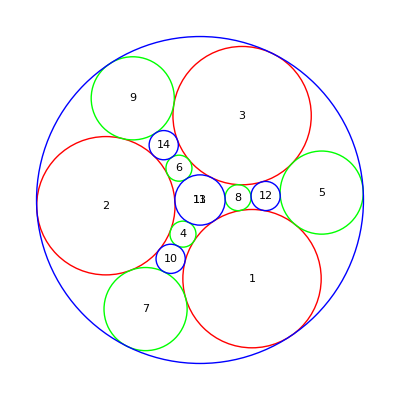

```mathematica
Triangulate[trefoil]
ShowCirclePacking[trefoil,{"X"->Red,"e"->Green,"f"->Blue}]
```

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

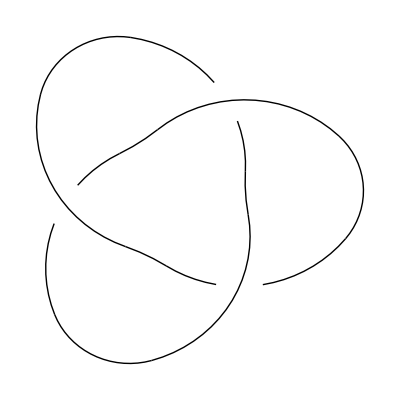

```mathematica
NewDrawPD[trefoil]
```

```mathematica
K=AddPositionsBound[DefaultDirichlet[Triangulate[trefoil]]]
```

{{{4,10,7,11,5,12,8,13},X,1.,1.10557+0.497886 ⅈ},{{6,14,9,11,7,10,4,13},X,0.126911,0.-4.49627×10^-17 ⅈ},{{8,12,5,11,9,14,6,13},X,0.0273216,0.168762+0.0278918 ⅈ},{{10,1,13,2},e,1.,-0.0630982-1.12514 ⅈ},{{12,1,11,3},e,0.0134417,0.190463+0.0623985 ⅈ},{{14,2,13,3},e,0.012888,0.139799-2.13371×10^-15 ⅈ},{{11,1,10,2},e,0.0793394,0.0698737+0.194054 ⅈ},{{13,1,12,3},e,0.0159258,0.21063+0.0170588 ⅈ},{{11,2,14,3},e,0.0112113,0.132193+0.0400356 ⅈ},{{1,4,2,7},f,1.,-0.88435+0.698465 ⅈ},{{1,7,2,9,3,5},f,0.044087,0.142618+0.0943423 ⅈ},{{1,5,3,8},f,0.0104318,0.203592+0.0424591 ⅈ},{{1,8,3,6,2,4},f,0.0793394,0.191622-0.0762907 ⅈ},{{2,6,3,9},f,0.00843294,0.133789+0.0204563 ⅈ}}

```mathematica
K=AddPositionsBound[DefaultDirichlet[Triangulate[trefoil]]]
K=PutInside[K,DefaultOuterFace[K]]
```

{{{4,10,7,11,5,12,8,13},X,1.,1.10557+0.497886 ⅈ},{{6,14,9,11,7,10,4,13},X,0.126911,0.-4.49627×10^-17 ⅈ},{{8,12,5,11,9,14,6,13},X,0.0273216,0.168762+0.0278918 ⅈ},{{10,1,13,2},e,1.,-0.0630982-1.12514 ⅈ},{{12,1,11,3},e,0.0134417,0.190463+0.0623985 ⅈ},{{14,2,13,3},e,0.012888,0.139799-2.13371×10^-15 ⅈ},{{11,1,10,2},e,0.0793394,0.0698737+0.194054 ⅈ},{{13,1,12,3},e,0.0159258,0.21063+0.0170588 ⅈ},{{11,2,14,3},e,0.0112113,0.132193+0.0400356 ⅈ},{{1,4,2,7},f,1.,-0.88435+0.698465 ⅈ},{{1,7,2,9,3,5},f,0.044087,0.142618+0.0943423 ⅈ},{{1,5,3,8},f,0.0104318,0.203592+0.0424591 ⅈ},{{1,8,3,6,2,4},f,0.0793394,0.191622-0.0762907 ⅈ},{{2,6,3,9},f,0.00843294,0.133789+0.0204563 ⅈ}}

{{{4,10,7,11,5,12,8,13},X,0.489216,0.47109-0.19742 ⅈ},{{6,14,9,11,7,10,4,13},X,0.426006,-0.478729+0.316682 ⅈ},{{8,12,5,11,9,14,6,13},X,0.27673,0.264804+0.673052 ⅈ},{{10,1,13,2},e,0.0832673,-0.0171294+0.101543 ⅈ},{{12,1,11,3},e,0.189399,0.674154+0.4501 ⅈ},{{14,2,13,3},e,0.0649932,-0.0142155+0.475763 ⅈ},{{11,1,10,2},e,0.391286,-0.358759-0.491757 ⅈ},{{13,1,12,3},e,0.0678716,0.289853+0.329362 ⅈ},{{11,2,14,3},e,0.168566,-0.156746+0.816525 ⅈ},{{1,4,2,7},f,0.105062,-0.107896-0.0634705 ⅈ},{{1,7,2,9,3,5},f,-1.,0.+0. ⅈ},{{1,5,3,8},f,0.0729911,0.426634+0.363027 ⅈ},{{1,8,3,6,2,4},f,0.138681,0.0856562+0.298256 ⅈ},{{2,6,3,9},f,0.0680179,-0.0712103+0.595944 ⅈ}}

```mathematica
K=AddGraphicsObjs[K,{.03}]
```

{{{4,10,7,11,5,12,8,13},X,0.489216,0.47109-0.19742 ⅈ,{{Circle[{0.253234,0.383609},0.381738,{-2.12025,-1.448}],Circle[{0.253234,0.383609},0.381738,{-1.29082,-0.30389}]},{Circle[{-0.155078,0.10451},0.493878,{-1.22995,0.331361}]}}},{{6,14,9,11,7,10,4,13},X,0.426006,-0.478729+0.316682 ⅈ,{{Circle[{0.0901458,-0.0295695},0.511887,{1.90075,2.31236}],Circle[{0.0901458,-0.0295695},0.511887,{2.42958,3.28892}]},{Circle[{0.0643909,0.473562},0.371632,{2.56933,4.27625}]}}},{{8,12,5,11,9,14,6,13},X,0.27673,0.264804+0.673052 ⅈ,{{Circle[{-0.131786,0.366684},0.41781,{0.0727543,0.488516}],Circle[{-0.131786,0.366684},0.41781,{0.632122,1.24275}]},{Circle[{0.295336,0.150549},0.444255,{1.07207,2.18626}]}}},{{10,1,13,2},e,0.0832673,-0.0171294+0.101543 ⅈ,{{Circle[{-0.712778,-1.19393},1.46807,{1.02134,1.13466}]}}},{{12,1,11,3},e,0.189399,0.674154+0.4501 ⅈ,{{Circle[{0.397611,0.338331},0.230427,{-0.30389,1.07207}]}}},{{14,2,13,3},e,0.0649932,-0.0142155+0.475763 ⅈ,{{Circle[{-0.222206,0.88249},0.452176,{-1.24085,-0.955334}]}}},{{11,1,10,2},e,0.391286,-0.358759-0.491757 ⅈ,{{Circle[{-0.0976376,-0.0574362},0.322047,{-2.99427,-1.22995}]}}},{{13,1,12,3},e,0.0678716,0.289853+0.329362 ⅈ,{{Circle[{0.805513,0.434997},0.521974,{-3.06884,-2.81023}]}}},{{11,2,14,3},e,0.168566,-0.156746+0.816525 ⅈ,{{Circle[{-0.0666752,0.557991},0.215726,{1.24275,2.56933}]}}},{{1,4,2,7},f,0.105062,-0.107896-0.0634705 ⅈ,{}},{{1,7,2,9,3,5},f,-1.,0.+0. ⅈ,{}},{{1,5,3,8},f,0.0729911,0.426634+0.363027 ⅈ,{}},{{1,8,3,6,2,4},f,0.138681,0.0856562+0.298256 ⅈ,{}},{{2,6,3,9},f,0.0680179,-0.0712103+0.595944 ⅈ,{}}}

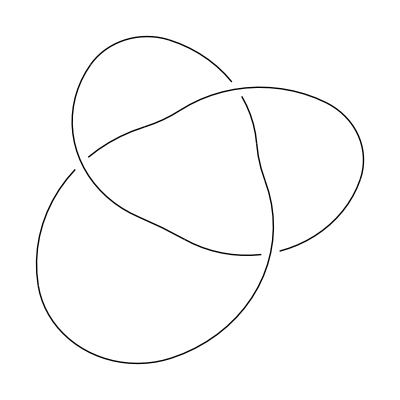

```mathematica
Draw[K]
```

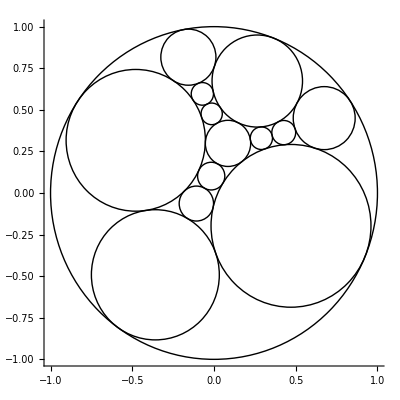

```mathematica
Graphics[Table[Circle[{Re[K[[i,centre]]],Im[K[[i,centre]]]},Abs[K[[i,r]]]],{i,Length@K}],Axes->True]
```

```mathematica
K=PD[X[1,4,2,3],X[3,1,4,2]]
Faces[K]
Function[{pd},Table[Map[pd⟦First@#,Last@#⟧&,Faces[pd]⟦i⟧],{i,Length@Faces[pd]}]][K]
```

```mathematica
(* PD Graph Manipulation *)

OtherVertex[pd_,coordinates_]:=
  Complement[
      Position[pd,
        Extract[pd,
          coordinates]],{coordinates}][[1]]

Faces[pd_]:=
  Select[
Flatten[
      Table[
NestWhileList[
          Function[{coordinates},{OtherVertex[pd,coordinates][[1]], Mod[OtherVertex[pd,coordinates][[2]]-1,Length[pd[[OtherVertex[pd,coordinates]⟦1⟧]]],1]
}]
,{i,j},Unequal,All,Infinity,-1
],{i,Length[pd]},{j,Length[pd[[i]]]}],1],
    Function[{face},
      face[[1]]==
        Sort[face][[1]]]]

Triangulate[pd_]:=(facelist=Faces[pd];
    Join[
(*crossings*)
Table[{Flatten[
            Table[{Length[pd]+
                  pd[[vertex,i]],
                Length[pd]+Length[Union[Flatten[pd,1,X]]]+
                  Position[facelist,face_/;MemberQ[face,{vertex,i}],1]⟦1,1⟧
},{i,Length[pd⟦vertex⟧]}]
],"X"},{vertex,Length[pd]}],
(*edges*)
      Table[{Flatten[
            Table[{Length[pd]+Length[Union[Flatten[pd,1,X]]]+
                  Position[facelist,
                      face_/;MemberQ[face,
                          Position[pd,edge,2][[
                            i]]],2][[1,
                    1]],
                Position[pd,edge,2][[i,
                  1]]},{i,Length[Position[pd,edge,2]]}]],
          "e"},{edge,Length[Union[Flatten[pd,1,X]]]}],
(*faces*)
      Table[{Flatten[
            Table[{facelist[[face,i,1]],
                Length[pd]+
                  Extract[pd,
                    facelist[[face,
                      i]]]},{i,
                Length[facelist[[
                    face]]]}]],"f"},{face,
          Length[facelist]}]])

GetOuterFace[triangulation_,edges_]:=
  Select[Range[Length[triangulation]],
      Function[v,triangulation⟦v,type⟧=="f"&&Union[
              Map[triangulation[[#]]&,triangulation⟦v,neighbours⟧],
              Select[triangulation,
#⟦type⟧=="e"&]⟦edges⟧]==Union[Map[triangulation⟦#⟧&,
                triangulation⟦v, neighbours⟧]]
]]⟦1⟧

NthOrderNeighbours[triangulation_,v_,0]:={v}
NthOrderNeighbours[triangulation_,v_,n_/;n>0]:=
  Apply[Union,
    Map[triangulation[[#,neighbours]]&,
      NthOrderNeighbours[triangulation,v,n-1]]]

DefaultOuterFace[triangulation_]:=
  Sort[Select[Range[Length[triangulation]],
        triangulation[[#,
              type]]=="f"&],
      Length[triangulation[[#1,
              neighbours]]]>=Length[
            triangulation[[#2,
              neighbours]]]&][[1]]
```

NthOrderNeighbours[triangulation, v, n] where v ϵ {1,2 ... Length[triangulation]}returns a list of neighbors by recursively calling the neighbors of v and their neighbors and so on for n orders and returning the union of the list.
This function is not used at all, it was perhaps useful when debugging.
NthOrderNeighbours[triangulation, v, 0] (*order of 0*) returns {v}.
NthOrderNeighbours[triangulation, v, 1] (*order of 1*) returns sorted triangulation⟦v, neighbors⟧ or the neighbors of v.
NthOrderNeighbours[triangulation, v, 2] (*order of 2*) returns the union of all of the neighbors of each vertex in triangulation⟦v, neighbors⟧ or the neighbors of the neighbors of v and the neighbors of v and v. This continues for higher orders.
One thing to note is that each higher order is a superset of the lower meaning all the elements in order 2 for example are contained in any order >2 for example. This is not always true for order 1 however. NthOrderNeighbours[triangulation, v, 1]  does not necessarily contain v (and doesn’t for any knot that can be drawn with DrawPD)

```mathematica
DefaultOuterFace[Triangulate[trefoil]]
(*returns the face with the most neighbors then the earliest in the triangulation, usefull later*)
```

#### Phase two: radii are added

Given three circles tangent to each other a, b, c with radii x, y, z respectively: CircleAngle[x,y,z] calculates the angle between geodesics connecting centers of circle c to a and b to a. This is represented visually in the following diagram where α is the value returned from CircleAngle[x,y,z].

```mathematica
trefoil =PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]];
DefaultDirichlet[Triangulate[trefoil]]
(*adds a radius field to each component of the triangulation*)
```

The circle packing algorithm essentially works by “relaxing” all of the radii into place. The relaxing is *mostly* monotonic and will always result in a decrease of radius. You begin with every component given a circle with radius of 1. A target angle is determined for each component too. The target is for the flower angle of a given vertex. Most components have a target angle of 2π but exactly three components will be given no target angle. They are the first, and the first two neighbors of the first component. This means one crossing, one edge, and one face will always have a radius of  1 by the end of the relaxation. DrawPD uses the Uniform Neighbour Model (UNM) for circle packing.

```mathematica
(* generalize to accept other types of vertices (v, etc.) *)

(* Circle Packing: Radii *)

CircleAngle[r_,r1_,r2_]:=
  ArcCos[((r1+r)^2+(r2+r)^2-(r1+r2)^2)/(2(r1+r)(r2+r))]

FlowerAngle[triangulation_,v_,radii_]:=
  Plus@@(CircleAngle[radii[[v]],#1,#2]&@@@
        Map[radii[[#]]&,
          Transpose[{triangulation[[v,
                neighbours]],
              RotateRight[
                triangulation[[v,
                  neighbours]]]}],{2}])

AdjustRadius[triangulation_,v_,targetAngle_,radii_]:=
  N[radii[[v]]((1-
              Cos[FlowerAngle[triangulation,v,radii]/
                  Length[triangulation[[v,
                      neighbours]]]]+
              Sqrt[2-2Cos[
                      FlowerAngle[triangulation,v,radii]/
                        Length[
                          triangulation[[v,
                            neighbours]]]]])/(1+
              Cos[FlowerAngle[triangulation,v,radii]/
                  Length[triangulation[[v,
                      neighbours]]]]))(Sqrt[
            2/(1-Cos[
                    targetAngle/
                      Length[triangulation[[v,
                          neighbours]]]])]-1)]

PackingStep[triangulation_,targetAngles_]:=( 
    radii=Table[Unique[radius],{Length[triangulation]}];
    Compile[Evaluate[radii],
      Evaluate[Table[
          If[targetAngles[[v]]==0,
            radii[[v]],
            AdjustRadius[triangulation,v,
              targetAngles[[v]],
              radii]],{v,Length[triangulation]}]]]
    )

GetRadii[triangulation_,targetAngles_,radii_]:=( 
    EvaluatedPackingStep=PackingStep[triangulation,targetAngles];
    NestWhile[EvaluatedPackingStep@@#&,radii,Unequal,2]
    )

DefaultDirichlet[triangulation_]:=
  AddField[triangulation,r,
    GetRadii[triangulation,
      ReplacePart[Table[2Pi,{Length[triangulation]}],
        0,{{1},{triangulation[[1,neighbours,1]]},{triangulation[[1,neighbours,2]]}}],
      Table[1,{Length[triangulation]}]]]
```

```mathematica
Module[{triangulation=Triangulate[trefoil],targetAngles},
targetAngles=ReplacePart[Table[2Pi,{Length[triangulation]}],
        0,{{1},{triangulation[[1,neighbours,
              1]]},{triangulation[[1,
              neighbours,2]]}}];
DefaultDirichlet[triangulation];
Print[Column[AddField[triangulation,r,targetAngles]]]
]
```

Just debugging stuff here.

Simply mushes two PD codes together incorrectly.

```mathematica
CompositeKnots[k1_PD,k2_PD]:=X@@@PD@@Union[List@@@List@@k1,List@@@List@@k2+2*Length@k1]
```

```mathematica
CompositeKnots[trefoil,figure8]
```

PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3],X[8,13,9,14],X[10,8,11,7],X[12,9,13,10],X[14,12,7,11]]

```mathematica
trefoil
```

PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]]

```mathematica
NewDrawPD[CompositeKnots[trefoil,figure8]]
```

#### Phase three: position field is added

DefaultDirichlet added radii, AddPositionsBound adds the position.
Note that even now, all the tangencies are in place and the knot could be drawn.
It will probably not match the PD code but nonetheless a diagram is produced from the PD code.

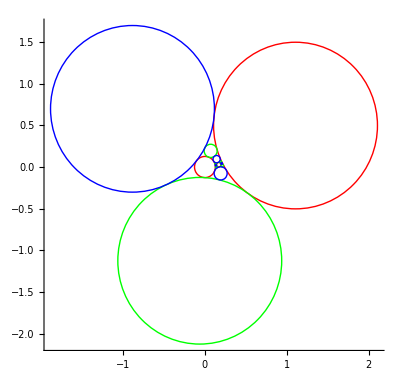

```mathematica
trefoil =PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]];
test=AddPositionsBound[DefaultDirichlet[Triangulate[trefoil]]];
(*displays the triangulation so far*)
Graphics[Table[{Switch[test⟦i,type⟧,"X",Red,"e",Green,"f",Blue],Circle[xyCoords[test⟦i,centre⟧],Abs@test⟦i,r⟧]},{i,Length@test}],Axes->True]
```

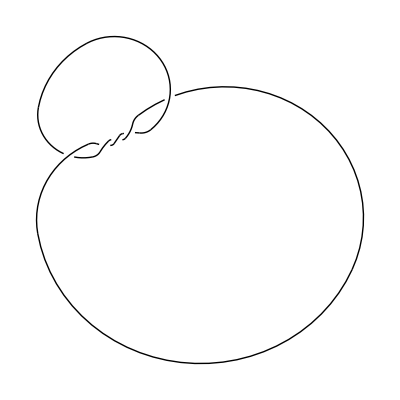

```mathematica
five1=PD[X[1,6,2,7],X[3,8,4,9],X[5,10,6,1],X[7,2,8,3],X[9,4,10,5]];
test=AddPositionsBound[DefaultDirichlet[Triangulate[five1]]];
test=AddGraphicsObjs[test,{0.01}];
Draw[test]
```

This means that the rest of the algorithm could be only necessary for drawing the knot for accuracy of PD
The Balance step that certain PD codes would get stuck on may not have even been necessary to draw the knot in any diagram.

```mathematica
(* Circle Packing: Positions *)

PlaceFlower[triangulation_,v_,neighbour_]:=
  For[w=triangulation[[v,neighbours,
        neighbour]];
    theta=Arg[(z[w]-
              z[v])/(triangulation[[w,
                r]]+
              triangulation[[v,r]])];
    lastr=triangulation[[w,r]];i=1,
    i<Length[triangulation[[v,
          neighbours]]],i++,
    w=triangulation[[v,neighbours,
        Mod[neighbour+i,
          Length[triangulation[[v,
              neighbours]]],1]]];
    currentr=triangulation[[w,r]];
    theta+=CircleAngle[
        triangulation[[v,r]],lastr,
        currentr];lastr=currentr;
    z[w]=z[v]+(triangulation[[v,r]]+
              currentr)Exp[I*theta];placed=Union[placed,{w}]]

PackCircles[triangulation_]:=(Clear[z];placed={};surrounded={};v1=1;z[v1]=0;
    placed=Union[placed,{v1}];
    v2=triangulation[[v1,neighbours,1]];
    z[v2]=triangulation[[v1,r]]+
        triangulation[[v2,r]];
    placed=Union[placed,{v2}];
    While[Length[placed]!=Length[triangulation],
      v=Complement[placed,
            surrounded][[1]];
      PlaceFlower[triangulation,v,
        Position[
            triangulation[[v,
              neighbours]],
            w_/;MemberQ[placed,w]][[1,
          1]]];surrounded=Union[surrounded,{v}]];
    Table[z[i],{i,Length[triangulation]}])

PackCirclesBound[triangulation_]:=(Clear[z];placed={};surrounded={};
    v1=Select[Range[Length[triangulation]],
          FlowerAngle[triangulation,#,
                FieldValues[triangulation,
                  r]]==2Pi&][[1\
]];z[v1]=0;placed=Union[placed,{v1}];
    v2=triangulation[[v1,neighbours,1]];
    z[v2]=triangulation[[v1,r]]+
        triangulation[[v2,r]];
    placed=Union[placed,{v2}];
    While[Length[placed]!=Length[triangulation],
      v=Select[Complement[placed,surrounded],
            FlowerAngle[triangulation,#,
                  FieldValues[triangulation,
                    r]]==2Pi&][[1\
]];
      PlaceFlower[triangulation,v,
        Position[
            triangulation[[v,
              neighbours]],
            w_/;MemberQ[placed,w]][[1,
          1]]];surrounded=Union[surrounded,{v}]];
    Table[z[i],{i,Length[triangulation]}])

AddPositions[triangulation_]:=
  AddField[triangulation,centre,PackCircles[triangulation]]

AddPositionsBound[triangulation_]:=
  AddField[triangulation,centre,PackCirclesBound[triangulation]]
```

#### Phase four: inversion and balancing

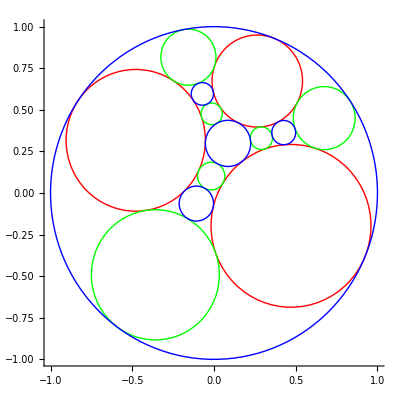

```mathematica
trefoil =PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]];
test=AddPositionsBound[DefaultDirichlet[Triangulate[trefoil]]];
test=PutInside[test,DefaultOuterFace[test]];
(*puts all the circles inside of this face while retaining tangencies, by inversion*)
(*displays the triangulation so far*)
Graphics[Table[{Switch[test⟦i,type⟧,"X",Red,"e",Green,"f",Blue],Circle[xyCoords[test⟦i,centre⟧],Abs@test⟦i,r⟧]},{i,Length@test}],Axes->True]
```

Just for fun, we can take a PD code, and rather than putting all the circles in the default outer face, we can generate a list of diagrams generated from using other faces.

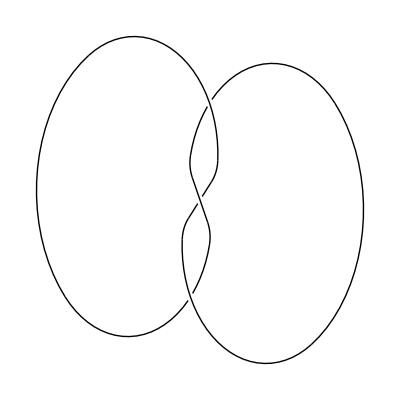
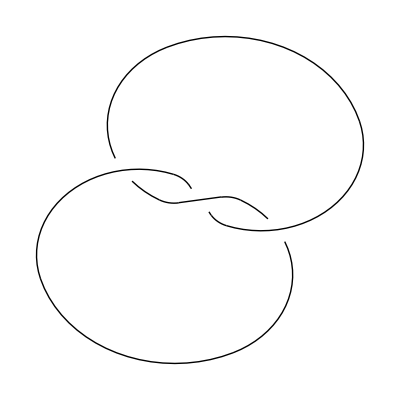
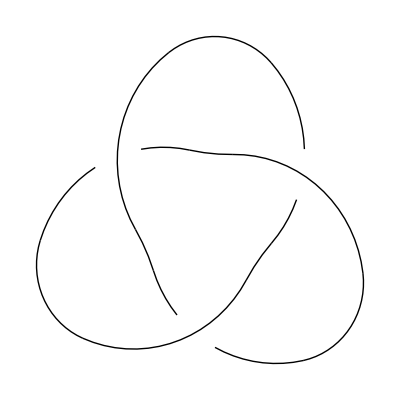
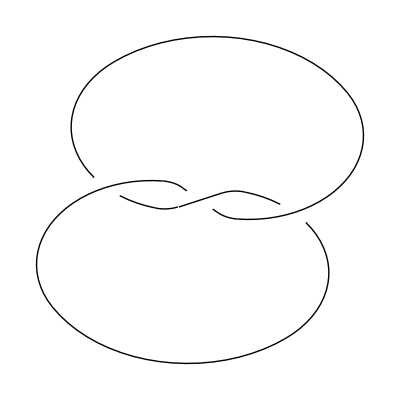
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WeirdDrawPD[pd_PD]:=Module[{list={},i,test},
For[i= Length[pd]+Length[Union[Flatten[pd,1,X]]]+1,i≤Length[Triangulate[pd]],i++,
test=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
test=PutInside[test,i];
test=ApplyFLMap[test,Moebius[Nest[BalanceStep[test,#]&,0,14]]];
test=AddGraphicsObjs[test,{DefaultGap[test]}];
AppendTo[list,test]
];
Return[Table[Draw[list⟦i⟧],{i,Length[list]}]]
]
WeirdDrawPD[trefoil]
```

Now that we have multiple diagrams, we can select the one who’s components’ minimum radius is largest.
We can do this by sorting the components by radius, then sorting the list of all triangulations by the radius of its first component.
Most of the time this is the same as using the regular DrawPD.

```mathematica
LargestMinrDrawPD[pd_PD]:=Module[{list={},i,test},
For[i= Length[pd]+Length[Union[Flatten[pd,1,X]]]+1,i≤Length[Triangulate[pd]],i++,
test=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
test=PutInside[test,i];
test=ApplyFLMap[test,Moebius[Nest[BalanceStep[test,#]&,0,14]]];
test=AddGraphicsObjs[test,{DefaultGap[test]}];
AppendTo[list,test]
];
(*Return[list];*)
Do[list⟦i⟧=Sort[list⟦i⟧,Abs[#1[[3]]]≤Abs[#2[[3]]]&],{i,Length@list}];
Return[Draw[Sort[list,Abs[#1[[1,r]]]≥Abs[#2[[1,r]]]&][[1]]]];
]
{LargestMinrDrawPD[twelve1024pd[[4]]],NewDrawPD[twelve1024pd[[4]],{Gap->0.01}]}
```

$Aborted

```mathematica
(* Fractional Linear Transformations *)

NewRadius[z_,radius_,{{a_,b_},{c_,d_}}]:=
  radius*Abs[a*d-b*c]/(Abs[c*z+d]^2-Abs[c]^2*radius^2)

NewPosition[z_,
    radius_,{{a_,b_},{c_,d_}}]:=((a*z+b)*Conjugate[c*z+d]-
        a*Conjugate[c]*radius^2)/((c*z+d)*Conjugate[c*z+d]-
        c*Conjugate[c]*radius^2)

ApplyFLMap[triangulation_,{{a_,b_},{c_,d_}}]:=(newRadii=
      Table[NewRadius[
          triangulation[[v,centre]],
          triangulation[[v,r]],{{a,b},{c,d}}],{v,Length[triangulation]}];
    newPositions=
      Table[NewPosition[
          triangulation[[v,centre]],
          triangulation[[v,r]],{{a,b},{c,d}}],{v,Length[triangulation]}];
    AddField[AddField[triangulation,r,newRadii],centre,newPositions])

Moebius[a_]:={{1,-a},{-Conjugate[a],1}}

ComposeMoebius[a_,b_]:=(a+b)/(1+a*Conjugate[b])
```

```mathematica
(* Inversion *)

PutInside[triangulation_,outerFace_]:=
  ApplyFLMap[
    triangulation,{{0,
        triangulation[[outerFace,
          r]]},{1,-triangulation[[
            outerFace,centre]]}}]
```

```mathematica
(* Balancing *)

BalanceStep[triangulation_,moebiusConst_]:=
  ComposeMoebius[
    Plus@@FieldValues[ApplyFLMap[triangulation,Moebius[moebiusConst]],centre]/
      Length[triangulation],moebiusConst]

BalanceMoebius[triangulation_]:=FixedPoint[BalanceStep[triangulation,#]&,0]

Balance[triangulation_]:=
  ApplyFLMap[triangulation,Moebius[BalanceMoebius[triangulation]]]
```

#### Phase 5: graphics

```mathematica
(* Graphics *)

xyCoords[z_]:=If[NumberQ[z],{Re[z],Im[z]},{Re[First@z],Im[First@z]}]
```

```mathematica
(* Graphics: Circle Packing *)

PackingGraphics[triangulation_]:=Graphics[Join[
      Map[
        Circle[xyCoords[#[[centre]]],
            Abs[#[[r]]]]&,triangulation],
      Table[Text[i,
          xyCoords[
            triangulation[[i,
              centre]]]],{i,Length[triangulation]}]],
    AspectRatio->1]
```

This code will find the path made by taking the first strand in the triangulation following it to other strands until it gets back to the first one.
It assigns an orientation to the knot and is also able to determine if the crossing is over or under. It records strands, crossing number, and defines an orientation.

```mathematica
K=PD[X[1,4,2,5],X[3,6,4,7],X[5,2,6,3],X[8,12,9,11],X[10,8,11,7],X[12,10,1,9]];
```

triangulation = {{{4,10,7,11,5,12,8,13},X},{{6,14,9,11,7,10,4,13},X},{{8,12,5,11,9,14,6,13},X},{{10,1,13,2},e},{{12,1,11,3},e},{{14,2,13,3},e},{{11,1,10,2},e},{{13,1,12,3},e},{{11,2,14,3},e},{{1,4,2,7},f},{{1,7,2,9,3,5},f},{{1,5,3,8},f},{{1,8,3,6,2,4},f},{{2,6,3,9},f}}
crossings = {{{4,5},{7,8}},{{6,7},{9,4}},{{8,9},{5,6}}}

path = {{1,1,1},{2,2,1},{3,1,1},{1,2,1},{2,1,1},{3,2,1}}

{4,over 2,9,under 3,8,over 1,7,under 2,6,over 3,5,under 1}

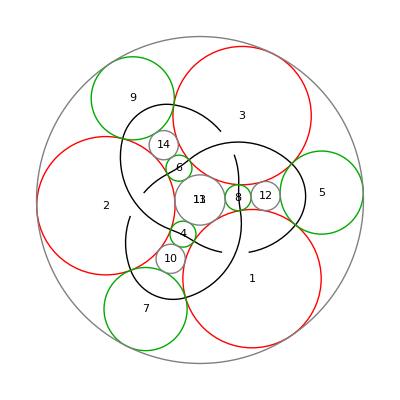

```mathematica
Module[{pd=trefoil,triangulation,crossings,path},
triangulation=Triangulate[pd];
crossings=Table[triangulation⟦i,neighbours,#⟧&/@ConnectedNeighbours[triangulation,i],{i,Length[pd]}];
path=NestWhileList[
Function[{coordinates},{OtherVertex[crossings,coordinates][[1]],OtherVertex[crossings,coordinates][[2]],  Mod[OtherVertex[crossings,coordinates][[3]]-1,2,1]}],{1,1,1},Unequal,All,Infinity,-1];

Print["triangulation = ",triangulation,"\ncrossings = ",crossings];
Print["path = ",path,"\n"];
Print[RotateLeft[Flatten[Table[
{If[path⟦i,2⟧==1,"under ","over "]<>ToString[path⟦i,1⟧],Extract[crossings,path⟦i⟧](*-Length@pd*)}
,{i,Length@path}]],1]];
Print[ShowCirclePacking[pd,{"X"->Red,"e"->Darker[Green],"f"->Gray,"ShowDiagram"->True}]];
]
```

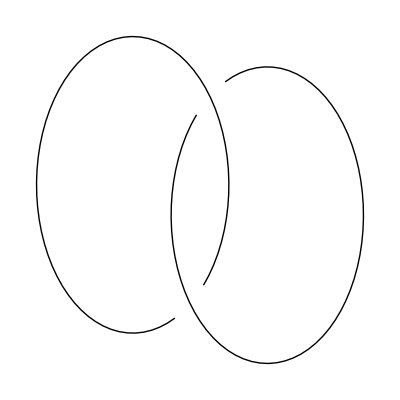

```mathematica
NewDrawPD[PD[X[1,4,2,3],X[3,2,4,1]]]
```

This block attempts to take the circle objects made from GetGraphicsObjs and take the orientation from above to place points along the circular arcs.

```mathematica
(*Nathan's code*)
CreateSegmentPoints[segments_,circle_]:=Table[circle⟦2⟧ Exp[I*(circle⟦3,2⟧+(i-1)(circle⟦3,1⟧-circle⟦3,2⟧)/segments)]+circle⟦1,1⟧+I circle⟦1,2⟧,{i,segments}]
DrawPDpts[pd_]:=Module[{t,crossings,path,circle,segments=1,points,circleObjs},
crossings=Table[Triangulate[pd]⟦i,neighbours,#⟧&/@ConnectedNeighbours[Triangulate[pd],i],{i,Length[pd]}];
t=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
t=PutInside[t,DefaultOuterFace[t]];
t=Balance[t];
t=AddGraphicsObjs[t,{0}];(*gap of 0*)
path=NestWhileList[
Function[{coordinates},{OtherVertex[crossings,coordinates][[1]],OtherVertex[crossings,coordinates][[2]], Mod[OtherVertex[crossings,coordinates][[3]]-1,2,1]}],{1,1,1},Unequal,All,Infinity,-1];
circleObjs=Table[t⟦i,graphicsObjs⟧,{i,3*Length@pd}];(*only gets the crossing and edge objects*)
(*To make sure the first point begins closest to the last point in the path*)
points=CreateSegmentPoints[segments,Extract[circleObjs,path⟦-1,1⟧]⟦2,1⟧];
(*main loop*)
Do[
If[path⟦j,2⟧==2(*over crossing*),
circle=Extract[circleObjs,path⟦j,1⟧]⟦2,1⟧;
If[EuclideanDistance[xyCoords[points⟦-1⟧],xyCoords[circle⟦2⟧*Exp[I*circle⟦3,2⟧]+circle⟦1,1⟧+I circle⟦1,2⟧]]≥EuclideanDistance[xyCoords[points⟦-1⟧],xyCoords[circle⟦2⟧*Exp[I*circle⟦3,1⟧]+circle⟦1,1⟧+I circle⟦1,2⟧]],
points=AppendTo[points,Map[{#,.2}&,CreateSegmentPoints[segments,Circle[{circle⟦1,1⟧,circle⟦1,2⟧},circle⟦2⟧,{circle⟦3,2⟧,circle⟦3,1⟧}]]]],(*flip a and b*)
points=AppendTo[points,Map[{#,.2}&,CreateSegmentPoints[segments,circle]]]
],
(*else if under crossing*)
circle=Extract[circleObjs,path⟦j,1⟧]⟦1,2⟧;
If[EuclideanDistance[xyCoords[points⟦-1⟧],xyCoords[circle⟦2⟧*Exp[I*circle⟦3,2⟧]+circle⟦1,1⟧+I circle⟦1,2⟧]]≥EuclideanDistance[xyCoords[points⟦-1⟧],xyCoords[circle⟦2⟧*Exp[I*circle⟦3,1⟧]+circle⟦1,1⟧+I circle⟦1,2⟧]],
points=AppendTo[points,Map[{#,-.2}&,CreateSegmentPoints[segments,Circle[{circle⟦1,1⟧,circle⟦1,2⟧},circle⟦2⟧,{circle⟦3,2⟧,circle⟦3,1⟧}]]]],(*flip a and b*)
points=AppendTo[points,Map[{#,-.2}&,CreateSegmentPoints[segments,circle]]]
];
circle=Extract[circleObjs,path⟦j,1⟧]⟦1,1⟧;
If[EuclideanDistance[xyCoords[points⟦-1⟧],xyCoords[circle⟦2⟧*Exp[I*circle⟦3,2⟧]+circle⟦1,1⟧+I circle⟦1,2⟧]]≥EuclideanDistance[xyCoords[points⟦-1⟧],xyCoords[circle⟦2⟧*Exp[I*circle⟦3,1⟧]+circle⟦1,1⟧+I circle⟦1,2⟧]],
points=AppendTo[points,Map[{#,-.2}&,CreateSegmentPoints[segments,Circle[{circle⟦1,1⟧,circle⟦1,2⟧},circle⟦2⟧,{circle⟦3,2⟧,circle⟦3,1⟧}]]]],(*flip a and b*)
points=AppendTo[points,Map[{#,-.2}&,CreateSegmentPoints[segments,circle]]]
]
];
(*collect strands*)
(*points=Flatten[points,1];*)
circle=Extract[circleObjs,Extract[crossings,path⟦j⟧]]⟦1,1⟧;
If[EuclideanDistance[xyCoords[points⟦-1⟧],xyCoords[circle⟦2⟧*Exp[I*circle⟦3,2⟧]+circle⟦1,1⟧+I circle⟦1,2⟧]]≥EuclideanDistance[xyCoords[points⟦-1⟧],xyCoords[circle⟦2⟧*Exp[I*circle⟦3,1⟧]+circle⟦1,1⟧+I circle⟦1,2⟧]],
points=AppendTo[points,Map[{#,0}&,CreateSegmentPoints[segments,Circle[{circle⟦1,1⟧,circle⟦1,2⟧},circle⟦2⟧,{circle⟦3,2⟧,circle⟦3,1⟧}]]]],(*flip a and b*)
points=AppendTo[points,Map[{#,0}&,CreateSegmentPoints[segments,circle]]]
]
,{j,Length@path}];
points=Flatten[points,1];
points=Drop[points,segments];(*Removes the initial point*)
points=Map[{Re[#⟦1⟧],Im[#⟦1⟧],#⟦2⟧}&,points];
points
]

exportPts[pts_]:=Module[{file},
ChoiceDialog["Save your knot"];
file=SystemDialogInput["FileSave",FileNameJoin[{$UserDocumentsDirectory,".mtx"}]];
file =ToString[file];
Export[file,pts]
]

viewKnot[pts_] :=Graphics3D[ptsToTubes[pts],PlotRange->All,ImageSize->Large]

viewStickKnot[pts_]:=Module[{points=pts},
AppendTo[points,pts⟦1⟧];
Graphics3D[{Thick,Line[points]},PlotRange->All,ImageSize->Large]
]

ptsToTubes[pts_]:=Module[{tubes,mids,points},
If[Length@pts≥3,
mids = Flatten[Table[{pts⟦i⟧,.5(pts⟦i⟧+pts⟦i+1⟧)},{i,Length@pts-1}],1];
AppendTo[mids,pts⟦-1⟧];
AppendTo[mids,.5(pts⟦-1⟧+pts⟦1⟧)];
AppendTo[mids,pts⟦1⟧];
points =Table[{mids⟦2i⟧,mids⟦2i+1⟧,mids⟦2i+2⟧},{i,Length@pts-1}];
AppendTo[points,{mids⟦-2⟧,mids⟦-1⟧,mids⟦2⟧}];
tubes:=Table[Tube[BSplineCurve[points⟦i⟧],0.02],{i,Length@pts}];
Return[tubes],
Return[Ball[{0,0,0},0]](*Returns a primitive but shows nothing*)
]
]
```

```mathematica
drawAnimColors[pts_]:=Module[{},
Animate[
,{}
]
]
```

```mathematica
?Animate
```

```mathematica
(* Knot Manipulation *)

ConnectedNeighbours[triangulation_,v_]:={{1,5},{3,7}}/;
    triangulation[[v,type]]=="X"
ConnectedNeighbours[triangulation_,v_]:={{2,4}}/;
    triangulation[[v,type]]=="e"
ConnectedNeighbours[triangulation_,v_]:={}/;
    triangulation[[v,type]]=="f"

Xunder=1;
Xover=2;

OtherEnd[triangulation_,v_,neighbour_]:=
  Select[Select[
          Map[triangulation[[v,
                neighbours,#]]&,
            ConnectedNeighbours[triangulation,v]],
          MemberQ[#,
              neighbour]&][[1]],# !=neighbour&][[1]]

AdjacentComponents[triangulation_,{v_,n_}]:=
  Select[Map[Take[#,2]&,
      Position[Table[
          Map[triangulation[[w,
                neighbours,#]]&,
            ConnectedNeighbours[triangulation,w]],{w,Length[triangulation]}],
        v]],Function[component,
      MemberQ[Map[
          triangulation[[v,
              neighbours,#]]&,
          ConnectedNeighbours[triangulation,v][[
            n]]],
        component[[1]]]]]

GetStrand[triangulation_,{v_,n_}]:=
  FixedPoint[
    Apply[Union,
        Append[Map[
            Function[component,
              AdjacentComponents[triangulation,component]],#],#]]&,{{v,n}}]

ListStrands[triangulation_]:=
  Union[Map[GetStrand[triangulation,#]&,
      Flatten[Table[{v,n},{v,Length[triangulation]},{n,
            Length[ConnectedNeighbours[triangulation,v]]}],1]]]
```

```mathematica
(* Graphics: Graphs *)

gapParam=1;

ArcCentre[z_,radius_,{z1_,z2_}]:=2*radius/Conjugate[Sign[z1-z]+Sign[z2-z]]

ArcRadius[z_,radius_,{z1_,z2_}]:=
  Sqrt[Abs[ArcCentre[z,radius,{z1,z2}]]^2-radius^2]

LinearProject[{v1_,v2_},w_]:=Re[v2-v1]*Cos[Arg[w]]+Im[v2-v1]*Sin[Arg[w]]

ArcProject[{v1_,v2_},o_]:=Mod[Arg[v2-o]-Arg[v1-o],2*Pi,-π]

ArcOrientation[z_,radius_,{z1_,z2_}]:=
  Sign[ArcProject[{radius*Sign[z1-z],radius*Sign[z2-z]},
      ArcCentre[z,radius,{z1,z2}]]]
```

```mathematica
(*find a way to consolidate the crossing functions*)

ArcCrossing[
    radius_,{arc1_,
      arc2_}]:=(Re[arc1]*Im[arc2]-Im[arc1]*Re[arc2]-
          Sign[Re[arc1]*Im[arc2]-Im[arc1]*Re[arc2]]*
            Sqrt[(Re[arc1]*Im[arc2]-Im[arc1]*Re[arc2])^2-
                Abs[arc1-arc2]^2*radius^2])/
      Abs[arc1-arc2]^2*(arc1-arc2)*I

ArcLineCrossing[
    radius_,{arc_,
      line_}]:=((Re[arc]*Re[line]+Im[arc]*Im[line]-
            Sign[Re[arc]*Re[line]+Im[arc]*Im[line]]*
              Sqrt[(Re[arc]*Re[line]+Im[arc]*Im[line])^2-
                  Abs[line]^2*radius^2])/Abs[line]^2)*line

Crossing[z_,radius_,{{z1_,z2_},{z3_,z4_}}]:=
  If[Sign[z1-z]+Sign[z2-z]==0,
    If[Sign[z3-z]+Sign[z4-z]==0,0,
      ArcLineCrossing[radius,{ArcCentre[z,radius,{z3,z4}],z2-z1}]],
    If[Sign[z3-z]+Sign[z4-z]==0,
      ArcLineCrossing[radius,{ArcCentre[z,radius,{z1,z2}],z4-z3}],
      ArcCrossing[
        radius,{ArcCentre[z,radius,{z1,z2}],ArcCentre[z,radius,{z3,z4}]}]]]

arcConst=10^(-5);

ArcDistance[z_,radius_,{z1_,z2_},{w1_,w2_}]:=
  Which[Sign[z1-z]+Sign[z2-z]==0,LinearProject[{w1,w2},z2-z1],
    Abs[ArcProject[{w1,w2},ArcCentre[z,radius,{z1,z2}]]](*==0*)(**)<
      arcConst(**),LinearProject[{w1,w2},
      ArcOrientation[z,
          radius,{z1,z2}]*I*((w1+w2)/2-
            ArcCentre[z,radius,{z1,z2}])],True,
    ArcOrientation[z,radius,{z1,z2}]*ArcRadius[z,radius,{z1,z2}]*
      ArcProject[{w1,w2},ArcCentre[z,radius,{z1,z2}]]]

GetArc[z_,radius_,{z1_,z2_},{w1_,w2_},{l1_,l2_}]:=
  Which[ArcDistance[z,radius,{z1,z2},{w1,w2}]<
      l1+l2,{},(*Mod[
          Arg[w1-ArcCentre[z,radius,{z1,z2}]]+
            ArcOrientation[z,radius,{z1,z2}]*l1/ArcRadius[z,radius,{z1,z2}],
          2*Pi,Arg[w1-ArcCentre[z,radius,{z1,z2}]]]==
        Mod[Arg[z2-ArcCentre[z,radius,{z1,z2}]]-
            ArcOrientation[z,radius,{z1,z2}]*l2/ArcRadius[z,radius,{z1,z2}],
          2*Pi,Arg[w1-ArcCentre[z,radius,{z1,z2}]]]*)(**)
      Abs[ArcProject[{w1,w2},ArcCentre[z,radius,{z1,z2}]]-
          l1/ArcRadius[z,radius,{z1,z2}]-l2/ArcRadius[z,radius,{z1,z2}]]<
      arcConst(**),{Line[{xyCoords[
            ArcCentre[z,radius,{z1,z2}]+
              ArcRadius[z,radius,{z1,z2}]*
                Exp[I*(Arg[w1-ArcCentre[z,radius,{z1,z2}]]+
                        ArcOrientation[z,radius,{z1,z2}]*
                          l1/ArcRadius[z,radius,{z1,z2}])]],
          xyCoords[
            ArcCentre[z,radius,{z1,z2}]+
              ArcRadius[z,radius,{z1,z2}]*
                Exp[I*(Arg[w2-ArcCentre[z,radius,{z1,z2}]]-
                        ArcOrientation[z,radius,{z1,z2}]*
                          l2/ArcRadius[z,radius,{z1,z2}])]]}]},
    True,{Circle[xyCoords[z+ArcCentre[z,radius,{z1,z2}]],
        ArcRadius[z,radius,{z1,z2}],
        Sort[{Mod[
              Arg[w1-ArcCentre[z,radius,{z1,z2}]]+
                ArcOrientation[z,radius,{z1,z2}]*
                  l1/ArcRadius[z,radius,{z1,z2}],2*Pi,
              Which[ArcOrientation[z,radius,{z1,z2}]>0,
                Arg[radius*Sign[z1]-ArcCentre[z,radius,{z1,z2}]]-Pi/2,
                ArcOrientation[z,radius,{z1,z2}]<0,
                Arg[radius*Sign[z2]-ArcCentre[z,radius,{z1,z2}]]-Pi/2]],
            Mod[Arg[w2-ArcCentre[z,radius,{z1,z2}]]-
                ArcOrientation[z,radius,{z1,z2}]*
                  l2/ArcRadius[z,radius,{z1,z2}],2*Pi,
              Which[ArcOrientation[z,radius,{z1,z2}]>0,
                Arg[radius*Sign[z1]-ArcCentre[z,radius,{z1,z2}]]-Pi/2,
                ArcOrientation[z,radius,{z1,z2}]<0,
                Arg[radius*Sign[z2]-ArcCentre[z,radius,{z1,z2}]]-Pi/2]]},
          Less]]}]

CircleParams[triangulation_,v_,
    n_]:={triangulation[[v,centre]],
    triangulation[[v,r]],
    Map[triangulation[[triangulation[[v,
            neighbours,#]],centre]]&,
      Map[ConnectedNeighbours[triangulation,
              v][[#]]&,n,{-1}],{-1}]}

ExtraGap[triangulation_,v_,neighbour_,gap_]:=
  If[MemberQ[
        Map[triangulation[[v,
              neighbours,#]]&,
          ConnectedNeighbours[triangulation,v][[
            Xunder]]],neighbour],
      Max[0,gap-
          Abs[Apply[ArcDistance,
              Join[CircleParams[triangulation,v,
                  Xunder],{{Apply[Crossing,
                      CircleParams[triangulation,v,{Xunder,Xover}]],
                    triangulation[[v,r]]*
                      Sign[triangulation[[neighbour,
                            centre]]-
                          triangulation[[v,
                            centre]]]}}]]]],0]/;
    triangulation[[v,type]]=="X"
ExtraGap[triangulation_,v_,neighbour_,gap_]:=
  If[MemberQ[
        Map[triangulation[[v,
              neighbours,#]]&,
          ConnectedNeighbours[triangulation,
              v][[1]]],neighbour],
      Max[0,ExtraGap[triangulation,OtherEnd[triangulation,v,neighbour],v,gap]-
          Apply[ArcDistance,
            Join[CircleParams[triangulation,v,
                1],{Map[
                  triangulation[[v,r]]*
                      Sign[triangulation[[#,
                            centre]]-
                          triangulation[[v,
                            centre]]]&,
                  Map[triangulation[[v,
                        neighbours,#]]&,
                    ConnectedNeighbours[triangulation,
                        v][[1]]]]}]]],0]/;
    triangulation[[v,type]]=="e"

DefaultGap[triangulation_]:=
  
  Min[Table[
      If[triangulation[[v,
            type]]=="X",
        Map[Abs[Apply[ArcDistance,
                Join[CircleParams[triangulation,v,
                    Xunder],{{triangulation[[v,
                          r]]*
                        Sign[triangulation[[#,
                              centre]]-
                            triangulation[[v,
                              r]]],
                      Apply[Crossing,
                        CircleParams[triangulation,v,{Xunder,Xover}]]}}]]]&,
          Map[triangulation[[v,
                neighbours,#]]&,
            ConnectedNeighbours[triangulation,v][[
              Xunder]]]],Infinity],{v,
        Length[triangulation]}]]

GetGraphicsObjs[triangulation_,v_,graphicsParams_]:=(*for crossings*)
{Join[ Apply[GetArc,
          Join[CircleParams[triangulation,v,
              Xunder],{{triangulation[[v,
                    r]]*
                  Sign[triangulation[[
                        triangulation[[v,neighbours,
                          ConnectedNeighbours[triangulation,
                              v][[Xunder,
                            1]]]],
                        centre]]-
                      triangulation[[v,
                        centre]]],
                Apply[Crossing,
                  CircleParams[triangulation,v,{Xunder,Xover}]]},{ExtraGap[
                  triangulation,
                  triangulation[[v,neighbours,
                    ConnectedNeighbours[triangulation,
                        v][[Xunder,
                      1]]]],v,
                  graphicsParams[[gapParam\
]]],
                graphicsParams[[gapParam\
]]}}]],
        Apply[GetArc,
          Join[CircleParams[triangulation,v,
              Xunder],{{Apply[Crossing,
                  CircleParams[triangulation,v,{Xunder,Xover}]],
                triangulation[[v,r]]*
                  Sign[triangulation[[triangulation[[v,neighbours,
                          ConnectedNeighbours[triangulation,
                              v][[Xunder,
                            2]]]],
                        centre]]-
                      triangulation[[v,
                        centre]]]},{graphicsParams[[gapParam]],
                ExtraGap[triangulation,
                  triangulation[[v,neighbours,
                    ConnectedNeighbours[triangulation,
                        v][[Xunder,
                      1]]]],v,
                  graphicsParams[[gapParam\
]]]}}]]],
      Apply[GetArc,
        Join[CircleParams[triangulation,v,
            Xover],{Map[
              triangulation[[v,r]]*
                  Sign[
                    triangulation[[#,
                        centre]]-
                      triangulation[[v,
                        centre]]]&,
              Map[triangulation[[v,
                    neighbours,#]]&,
                ConnectedNeighbours[triangulation,v][[
                  Xover]]]],
            Map[ExtraGap[triangulation,#,v,
                  graphicsParams[[
                    gapParam]]]&,
              Map[triangulation[[v,
                    neighbours,#]]&,
                ConnectedNeighbours[triangulation,v][[
                  Xover]]]]}]]}/;
    triangulation[[v,type]]=="X"
GetGraphicsObjs[triangulation_,v_,graphicsParams_]:= (*for edges*)
{Apply[GetArc, Join[CircleParams[triangulation,v,
            1],{Map[triangulation[[v,r]]*
                  Sign[triangulation[[#,
                        centre]]-
                      triangulation[[v,
                        centre]]]&,
              Map[triangulation[[v,
                    neighbours,#]]&,
                ConnectedNeighbours[triangulation,
                    v][[1]]]],
            Map[ExtraGap[triangulation,#,v,
                  graphicsParams[[1]]]&,
              Map[triangulation[[v,
                    neighbours,#]]&,
                ConnectedNeighbours[triangulation,
                    v][[1]]]]}]]}/;
    triangulation[[v,type]]=="e"
GetGraphicsObjs[triangulation_,v_,graphicsParams_]:=(*for faces*)
{}/; triangulation[[v,type]]=="f"

AddGraphicsObjs[triangulation_,graphicsParams_]:=
  AddField[triangulation,graphicsObjs,
    Table[GetGraphicsObjs[triangulation,v,graphicsParams],{v,
        Length[triangulation]}]]

Draw[triangulation_]:=
  Graphics[Flatten[
      FieldValues[triangulation,graphicsObjs]],{AspectRatio->1}]
```

```mathematica
(* Colours *)

colourList={RGBColor[0,0,0],RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[1,1,0],
      RGBColor[0,0,1],RGBColor[0.5,0.25,0],RGBColor[1,0,1],
      RGBColor[1,0.5,0.5],RGBColor[1,0.5,0],RGBColor[0.5,0.5,0.5]};

AddColour[triangulation_,components_,colour_]:=
  Insert[Insert[triangulation,colour,
      Table[{components[[i,1]],
          graphicsObjs,components[[i,2]],
          1},{i,Length[components]}]],RGBColor[0,0,0],
    Table[{components[[i,1]],
        graphicsObjs,
        components[[i,2]],-1},{i,
        Length[components]}]]

ColourStrands[triangulation_,colouredStrands_]:=
  Fold[AddColour[#1,#2[[1]],#2[[2]]]&,triangulation,
    Transpose[{ListStrands[triangulation],
        Take[Fold[
            Insert[#1,#2[[2]],#2[[1]]]&,
            Select[colourList,
              FreeQ[
If[Length[colouredStrands]==0,{},Transpose[colouredStrands][[2]]
],#]&],colouredStrands],
          Length[ListStrands[triangulation]]]}]]

OuterFace="OuterFace";
(* Commented out by Dror: Gap="Gap"; *)
Colour="Colour";
StrandColour="StrandColour";

(* Dror: Add line and pd -> pd_PD *)
DrawPD[L_] := DrawPD[PD[L]]
DrawPD[L_,options_] := DrawPD[PD[L],options]
DrawPD[pd_PD]:=( CreditMessage["DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004."];
    t=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
    t=PutInside[t,DefaultOuterFace[t]];t=Balance[t];
    t=AddGraphicsObjs[t,{DefaultGap[t]}];
t=ColourStrands[t,{}];
Draw[t])


DrawPD[pd_PD,options_]:=(optionsList=Map[Apply[List,#]&,options];
    t=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
    t=PutInside[t,
        Which[Length[
              Select[optionsList,#[[1]]\
==OuterFace&]]==0,DefaultOuterFace[t],
          Depth[Select[
                  optionsList,#[[1]]\
==OuterFace&][[1,2]]]==1,
          Select[optionsList,#[[1]]\
==OuterFace&][[1,2]],True,
          GetOuterFace[t,
            Select[optionsList,#[[1]]\
==OuterFace&][[1,2]]]]];
    t=Balance[t];
    graphicsParams={If[
          Length[Select[
                optionsList,#[[1]]\
==Gap&]]==0,DefaultGap[t],
          Select[optionsList,#[[1]]\
==Gap&][[1,2]]]};
    t=AddGraphicsObjs[t,graphicsParams];
    t=If[Length[
            Select[optionsList,#[[1]]\
==Colour&]]==0,t,
        ColourStrands[t,
          If[Length[
                Select[optionsList,#[[1]]\
==StrandColour&]]==0,{},
            MapAt[Position[
                    ListStrands[t],{#+Length[pd],1}][[1,
                  1]]&,
              Select[optionsList,#[[1]]\
==StrandColour&][[1,2]],
              Table[{1,i},{i,
                  Length[Select[
                        optionsList,#[[1\
]]==StrandColour&][[1,
                      2]]]}]]]]];Draw[t])
```

I have added a ShowCirclePacking function which uses the PackingGraphics function. The argument is a PD code.
I also added NewDrawPD which is much faster than the old DrawPD but not as “Balanced”. The knot may not have machine precision placed strands but most computers can’t display more than 4 magnitudes worth of precision on a display. Thus, the knot itself will most likely display correctly with all the tangencies in the right place, and except for extremely large knots the output will be graphically identical.
ShowTriangulationGraph[PD] will show the drawn diagram as usual but on top of the triangulation made by the circle packing. each component is represented as a point.

```mathematica
ShowTriangulationGraph[trefoil]
```

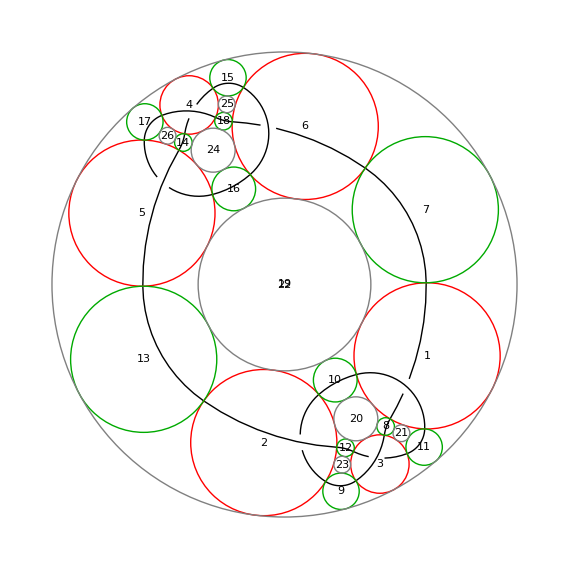

```mathematica
ShowCirclePacking[K,{"X"->Red,"e"->Darker[Green],"f"->Gray,"ShowDiagram"->True}]
```

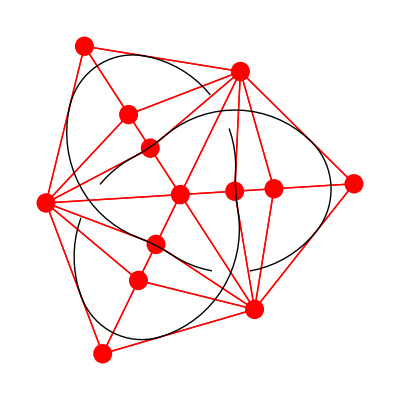

```mathematica
ShowTriangulationGraph[trefoil]
```

```mathematica
(*Nathan's edits*)
ShowCirclePacking[L_]:= ShowCirclePacking[PD[L]]
ShowCirclePacking[pd_PD]:= (
t=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
    t=PutInside[t,DefaultOuterFace[t]];
t=ApplyFLMap[t,Moebius[Nest[BalanceStep[t,#]&,0,100]]];
Graphics[Join[Table[{Circle[xyCoords[t⟦i,centre⟧],Abs@t⟦i,r⟧]},{i,Length@t}],
Table[Text[i,
          xyCoords[t[[i,centre]]]],{i,Length[t]}]]]
)


ShowCirclePacking[pd_PD,options_]:= Module[{optionsList= Map[Apply[List,#]&,options],newt},
t=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
    t=PutInside[t,DefaultOuterFace[t]];
t=ApplyFLMap[t,Moebius[Nest[BalanceStep[t,#]&,0,100]]];
t= AddGraphicsObjs[t,{DefaultGap[t]}];
Switch[Length@optionsList,
3,
If[optionsList⟦1,1⟧=="X"&&optionsList⟦2,1⟧=="e"&&optionsList⟦3,1⟧=="f",
Graphics[Join[Table[{Switch[t⟦i,type⟧,optionsList⟦1,1⟧,optionsList⟦1,2⟧,optionsList⟦2,1⟧,optionsList⟦2,2⟧,optionsList⟦3,1⟧,optionsList⟦3,2⟧, _, Black],Circle[xyCoords[t⟦i,centre⟧],Abs@t⟦i,r⟧]},{i,Length@t}],{Black},
Table[Text[i,
          xyCoords[t[[i,centre]]]],{i,Length[t]}]]]
],
4,
If[optionsList⟦1,1⟧=="X"&&optionsList⟦2,1⟧=="e"&&optionsList⟦3,1⟧=="f"&&optionsList⟦4,1⟧=="ShowDiagram"&&optionsList⟦4,2⟧==True,
newt=Flatten[FieldValues[t,graphicsObjs]];
(*for composite knots*)
Do[While[newt⟦i,3,2⟧-newt⟦i,3,1⟧>Pi,newt⟦i,3,2⟧-=2Pi];
While[newt⟦i,3,1⟧-newt⟦i,3,2⟧>Pi,newt⟦i,3,2⟧-=2Pi];
,{i,Length@newt}];
Graphics[Join[newt,
Table[{Switch[t⟦i,type⟧,optionsList⟦1,1⟧,optionsList⟦1,2⟧,optionsList⟦2,1⟧,optionsList⟦2,2⟧,optionsList⟦3,1⟧,optionsList⟦3,2⟧, _, Black],Circle[xyCoords[t⟦i,centre⟧],Abs@t⟦i,r⟧]},{i,Length@t}],{Black},
Table[Text[i,
          xyCoords[t[[i,centre]]]],{i,Length[t]}]]]
]
]
]

(*shows the graph too*)
ShowTriangulationGraph[pd_PD]:= Module[{t,defaultGap,g,defaultOuterFace},
t=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
defaultOuterFace=DefaultOuterFace[t];
    t=PutInside[t,defaultOuterFace];
t=ApplyFLMap[t,Moebius[Nest[BalanceStep[t,#]&,0,100]]];
defaultGap=DefaultGap[t]/2.0;
g=Join[Table[If[defaultOuterFace≠i,
Disk[xyCoords[t⟦i,centre⟧],defaultGap]],{i,Length@t}],
Table[If [(t⟦i,neighbours,j⟧≠ defaultOuterFace)&&(i≠defaultOuterFace),
Line[{xyCoords[t⟦i,centre⟧],xyCoords[t⟦t⟦i,neighbours,j⟧,centre⟧]}]]
,{i,Length@t},{j,Length[t⟦i,neighbours⟧]}]];
t=AddGraphicsObjs[t,{DefaultGap[t]}];
t=Flatten[FieldValues[t,graphicsObjs]];
(*for composite knots*)
Do[While[t⟦i,3,2⟧-t⟦i,3,1⟧>Pi,t⟦i,3,2⟧-=2Pi];
While[t⟦i,3,1⟧-t⟦i,3,2⟧>Pi,t⟦i,3,2⟧-=2Pi];
,{i,Length@t}];
Graphics[Join[{Red,g},{Black,t}],AspectRatio->1]
]

NewDrawPD[L_] := NewDrawPD[PD[L]]
NewDrawPD[L_,options_] := NewDrawPD[PD[L],options]
NewDrawPD[pd_PD]:=( 
    CreditMessage["DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004."];
    t=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
    t=PutInside[t,DefaultOuterFace[t]];
(*same as drawPD but replaces the Balance function*)
t=ApplyFLMap[t,Moebius[Nest[BalanceStep[t,#]&,0,100]]];
    t=AddGraphicsObjs[t,{DefaultGap[t]}];
(*t=ColourStrands[t,{}];*)
t=Flatten[FieldValues[t,graphicsObjs]];
(*for composite knots*)
(*Do[While[t⟦i,3,2⟧-t⟦i,3,1⟧>Pi,t⟦i,3,2⟧-=2Pi];
While[t⟦i,3,1⟧-t⟦i,3,2⟧>Pi,t⟦i,3,2⟧-=2Pi];
,{i,Length@t}];*)
 Graphics[t,AspectRatio->1]
)

NewDrawPD[pd_PD,options_]:=(optionsList=Map[Apply[List,#]&,options];
    t=AddPositionsBound[DefaultDirichlet[Triangulate[pd]]];
    t=PutInside[t,
        Which[Length[
              Select[optionsList,#[[1]]\
==OuterFace&]]==0,DefaultOuterFace[t],
          Depth[Select[
                  optionsList,#[[1]]\
==OuterFace&][[1,2]]]==1,
          Select[optionsList,#[[1]]\
==OuterFace&][[1,2]],True,
          GetOuterFace[t,
            Select[optionsList,#[[1]]\
==OuterFace&][[1,2]]]]];
   t=ApplyFLMap[t,Moebius[Nest[BalanceStep[t,#]&,0,100]]];
    graphicsParams={If[
          Length[Select[
                optionsList,#[[1]]\
==Gap&]]==0,DefaultGap[t],
          Select[optionsList,#[[1]]\
==Gap&][[1,2]]]};
    t=AddGraphicsObjs[t,graphicsParams];
    t=If[Length[
            Select[optionsList,#[[1]]\
==Colour&]]==0,t,
        ColourStrands[t,
          If[Length[
                Select[optionsList,#[[1]]\
==StrandColour&]]==0,{},
            MapAt[Position[
                    ListStrands[t],{#+Length[pd],1}][[1,
                  1]]&,
              Select[optionsList,#[[1]]\
==StrandColour&][[1,2]],
              Table[{1,i},{i,
                  Length[Select[
                        optionsList,#[[1\
]]==StrandColour&][[1,
                      2]]]}]]]]];
t=Flatten[FieldValues[t,graphicsObjs]];
(*for composite knots*)
Do[While[t⟦i,3,2⟧-t⟦i,3,1⟧>Pi,t⟦i,3,2⟧-=2Pi];
While[t⟦i,3,1⟧-t⟦i,3,2⟧>Pi,t⟦i,3,2⟧-=2Pi];
,{i,Length@t}];
 Graphics[t,AspectRatio->1])
```

Here are all the PD codes I have for the knot 10_78. Through the examples below you can see how NewDrawPD draws all the PD codes where DrawPD sometimes fails.
Below that is 12_1024 PD codes.

```mathematica
ten78pd={PD[X[1,8,2,9],X[11,1,12,20],X[9,2,10,3],X[3,7,4,6],X[17,4,18,5],X[5,16,6,17],X[7,10,8,11],X[15,12,16,13],X[13,18,14,19],X[19,14,20,15]],
PD[X[1,6,2,7],X[9,1,10,20],X[7,2,8,3],X[3,16,4,17],X[15,4,16,5],X[5,8,6,9],X[13,10,14,11],X[11,18,12,19],X[19,12,20,13],X[17,15,18,14]],
PD[X[1,8,2,9],X[17,20,18,1],X[9,2,10,3],X[3,7,4,6],X[15,4,16,5],X[5,14,6,15],X[7,10,8,11],X[11,18,12,19],X[19,12,20,13],X[13,17,14,16]],
PD[X[1,5,2,4],X[17,20,18,1],X[13,2,14,3],X[3,12,4,13],X[5,18,6,19],X[19,6,20,7],X[7,10,8,11],X[15,8,16,9],X[9,16,10,17],X[11,15,12,14]],
PD[X[1,6,2,7],X[9,1,10,20],X[7,2,8,3],X[3,14,4,15],X[13,4,14,5],X[5,8,6,9],X[19,11,20,10],X[11,16,12,17],X[17,12,18,13],X[15,18,16,19]],
PD[X[1,4,2,5],X[9,1,10,20],X[7,2,8,3],X[3,8,4,9],X[5,16,6,17],X[15,6,16,7],X[19,11,20,10],X[11,14,12,15],X[17,12,18,13],X[13,18,14,19]],
PD[X[1,6,2,7],X[17,20,18,1],X[7,2,8,3],X[3,14,4,15],X[13,4,14,5],X[5,8,6,9],X[9,18,10,19],X[19,10,20,11],X[11,17,12,16],X[15,13,16,12]],
PD[X[9,20,10,1],X[1,16,2,17],X[17,2,18,3],X[3,6,4,7],X[13,4,14,5],X[5,14,6,15],X[7,13,8,12],X[11,9,12,8],X[19,10,20,11],X[15,18,16,19]],
PD[X[1,5,2,4],X[17,20,18,1],X[13,2,14,3],X[3,12,4,13],X[5,18,6,19],X[19,6,20,7],X[7,17,8,16],X[11,8,12,9],X[9,14,10,15],X[15,10,16,11]],
PD[X[1,6,2,7],X[9,1,10,20],X[7,2,8,3],X[3,14,4,15],X[13,4,14,5],X[5,8,6,9],X[17,10,18,11],X[11,18,12,19],X[15,13,16,12],X[19,16,20,17]],
PD[X[1,4,2,5],X[17,20,18,1],X[9,2,10,3],X[3,10,4,11],X[5,9,6,8],X[15,6,16,7],X[7,14,8,15],X[11,18,12,19],X[19,12,20,13],X[13,17,14,16]],
PD[X[1,4,2,5],X[9,1,10,20],X[7,2,8,3],X[3,8,4,9],X[5,14,6,15],X[13,6,14,7],X[19,11,20,10],X[11,16,12,17],X[17,12,18,13],X[15,18,16,19]],
PD[X[1,4,2,5],X[17,20,18,1],X[7,2,8,3],X[3,8,4,9],X[5,14,6,15],X[13,6,14,7],X[9,18,10,19],X[19,10,20,11],X[11,17,12,16],X[15,13,16,12]],
PD[X[1,4,2,5],X[17,20,18,1],X[11,2,12,3],X[3,12,4,13],X[5,11,6,10],X[9,7,10,6],X[7,16,8,17],X[15,8,16,9],X[13,18,14,19],X[19,14,20,15]]};
```

```mathematica
Timing[Map[NewDrawPD[#,{Gap->0.03}]&,ten78pd]]
```

```mathematica
twelve1024pd={PD[X[6,2,7,1],X[24,20,1,19],X[2,15,3,16],X[16,3,17,4],X[4,17,5,18],X[14,5,15,6],X[18,8,19,7],X[8,14,9,13],X[20,10,21,9],X[10,24,11,23],X[22,12,23,11],X[12,22,13,21]],
PD[X[6,2,7,1],X[24,14,1,13],X[2,17,3,18],X[14,3,15,4],X[4,15,5,16],X[16,5,17,6],X[12,8,13,7],X[8,22,9,21],X[20,10,21,9],X[10,20,11,19],X[22,12,23,11],X[18,24,19,23]],
PD[X[24,12,1,11],X[16,2,17,1],X[2,16,3,15],X[14,4,15,3],X[4,18,5,17],X[10,6,11,5],X[6,21,7,22],X[22,7,23,8],X[8,23,9,24],X[20,9,21,10],X[12,20,13,19],X[18,14,19,13]],
PD[X[6,2,7,1],X[24,12,1,11],X[2,15,3,16],X[12,3,13,4],X[4,13,5,14],X[14,5,15,6],X[18,8,19,7],X[8,22,9,21],X[20,10,21,9],X[10,20,11,19],X[16,24,17,23],X[22,18,23,17]],
PD[X[6,2,7,1],X[24,18,1,17],X[2,13,3,14],X[14,3,15,4],X[4,15,5,16],X[12,5,13,6],X[16,8,17,7],X[8,22,9,21],X[20,10,21,9],X[10,20,11,19],X[22,12,23,11],X[18,24,19,23]],
PD[X[24,7,1,8],X[14,2,15,1],X[2,18,3,17],X[16,4,17,3],X[4,16,5,15],X[20,6,21,5],X[6,12,7,11],X[8,21,9,22],X[22,9,23,10],X[10,23,11,24],X[12,20,13,19],X[18,14,19,13]],
PD[X[6,2,7,1],X[24,20,1,19],X[2,15,3,16],X[16,3,17,4],X[4,17,5,18],X[14,5,15,6],X[18,8,19,7],X[8,14,9,13],X[22,10,23,9],X[10,22,11,21],X[20,12,21,11],X[12,24,13,23]],
PD[X[6,2,7,1],X[24,14,1,13],X[2,17,3,18],X[14,3,15,4],X[4,15,5,16],X[16,5,17,6],X[12,8,13,7],X[8,20,9,19],X[22,10,23,9],X[10,22,11,21],X[20,12,21,11],X[18,24,19,23]],
PD[X[24,12,1,11],X[14,2,15,1],X[2,18,3,17],X[16,4,17,3],X[4,16,5,15],X[10,6,11,5],X[6,21,7,22],X[22,7,23,8],X[8,23,9,24],X[20,9,21,10],X[12,20,13,19],X[18,14,19,13]],
PD[X[6,2,7,1],X[24,12,1,11],X[2,15,3,16],X[12,3,13,4],X[4,13,5,14],X[14,5,15,6],X[20,8,21,7],X[8,20,9,19],X[18,10,19,9],X[10,22,11,21],X[16,24,17,23],X[22,18,23,17]],
PD[X[6,2,7,1],X[24,18,1,17],X[2,13,3,14],X[14,3,15,4],X[4,15,5,16],X[12,5,13,6],X[16,8,17,7],X[8,20,9,19],X[22,10,23,9],X[10,22,11,21],X[20,12,21,11],X[18,24,19,23]],
PD[X[24,7,1,8],X[16,2,17,1],X[2,16,3,15],X[14,4,15,3],X[4,18,5,17],X[20,6,21,5],X[6,12,7,11],X[8,21,9,22],X[22,9,23,10],X[10,23,11,24],X[12,20,13,19],X[18,14,19,13]],
PD[X[6,2,7,1],X[24,20,1,19],X[2,17,3,18],X[14,3,15,4],X[4,15,5,16],X[16,5,17,6],X[18,8,19,7],X[8,14,9,13],X[20,10,21,9],X[10,24,11,23],X[22,12,23,11],X[12,22,13,21]],
PD[X[6,2,7,1],X[24,14,1,13],X[2,15,3,16],X[16,3,17,4],X[4,17,5,18],X[14,5,15,6],X[12,8,13,7],X[8,22,9,21],X[20,10,21,9],X[10,20,11,19],X[22,12,23,11],X[18,24,19,23]],
PD[X[24,12,1,11],X[16,2,17,1],X[2,16,3,15],X[14,4,15,3],X[4,18,5,17],X[10,6,11,5],X[6,23,7,24],X[20,7,21,8],X[8,21,9,22],X[22,9,23,10],X[12,20,13,19],X[18,14,19,13]],
PD[X[6,2,7,1],X[24,12,1,11],X[2,13,3,14],X[14,3,15,4],X[4,15,5,16],X[12,5,13,6],X[18,8,19,7],X[8,22,9,21],X[20,10,21,9],X[10,20,11,19],X[16,24,17,23],X[22,18,23,17]],
PD[X[6,2,7,1],X[24,18,1,17],X[2,15,3,16],X[12,3,13,4],X[4,13,5,14],X[14,5,15,6],X[16,8,17,7],X[8,22,9,21],X[20,10,21,9],X[10,20,11,19],X[22,12,23,11],X[18,24,19,23]],
PD[X[24,10,1,9],X[14,1,15,2],X[2,11,3,12],X[12,3,13,4],X[4,13,5,14],X[18,6,19,5],X[6,22,7,21],X[20,8,21,7],X[8,20,9,19],X[10,16,11,15],X[16,24,17,23],X[22,18,23,17]],
PD[X[6,2,7,1],X[24,20,1,19],X[2,17,3,18],X[14,3,15,4],X[4,15,5,16],X[16,5,17,6],X[18,8,19,7],X[8,14,9,13],X[22,10,23,9],X[10,22,11,21],X[20,12,21,11],X[12,24,13,23]],
PD[X[6,2,7,1],X[24,14,1,13],X[2,15,3,16],X[16,3,17,4],X[4,17,5,18],X[14,5,15,6],X[12,8,13,7],X[8,20,9,19],X[22,10,23,9],X[10,22,11,21],X[20,12,21,11],X[18,24,19,23]],
PD[X[24,12,1,11],X[14,2,15,1],X[2,18,3,17],X[16,4,17,3],X[4,16,5,15],X[10,6,11,5],X[6,23,7,24],X[20,7,21,8],X[8,21,9,22],X[22,9,23,10],X[12,20,13,19],X[18,14,19,13]],
PD[X[6,2,7,1],X[24,12,1,11],X[2,13,3,14],X[14,3,15,4],X[4,15,5,16],X[12,5,13,6],X[20,8,21,7],X[8,20,9,19],X[18,10,19,9],X[10,22,11,21],X[16,24,17,23],X[22,18,23,17]],
PD[X[6,2,7,1],X[24,18,1,17],X[2,15,3,16],X[12,3,13,4],X[4,13,5,14],X[14,5,15,6],X[16,8,17,7],X[8,20,9,19],X[22,10,23,9],X[10,22,11,21],X[20,12,21,11],X[18,24,19,23]],
PD[X[24,10,1,9],X[14,1,15,2],X[2,11,3,12],X[12,3,13,4],X[4,13,5,14],X[20,6,21,5],X[6,20,7,19],X[18,8,19,7],X[8,22,9,21],X[10,16,11,15],X[16,24,17,23],X[22,18,23,17]]};
```

```mathematica
drawnTwelve1024pd=Timing[Map[NewDrawPD[#,{Gap->0.01}]&,twelve1024pd]]
```